```mathematica
mP=1.67*10^(-24); (*g*)
kB=1.38*10^(-16); (*in cgs*)
G=6.67*10^(-8);   (*in cgs*)
h=6.63*10^(-27); (*in cgs*)
Msun=1.989*10^33;
Rsun=6.9598*10^10;
Lsun=3.8418*10^33;
c=3*10^10;   (*cm/s*)
σSB=5.67*10^(-5); 
a=4*σSB/c;   
γ=5/3 ;
mu=0.62;
```

```mathematica
Polinomi=Table[q^i,{i,0,10}];
```

```mathematica
SolarModel0=Import["C:\\Users\\Pigkappa\\Dropbox\\fisica\\PhD\\SolarRotation\\BalbusEquation\\SolarModelBS2005-AGS,OP","Table"];

SolarModel=Drop[SolarModel0,1];
SolarModel=Drop[SolarModel,-3];

RadiusMass=Table[{ Rsun*SolarModel[[All,2]][[i]],Msun*SolarModel[[All,1]][[i]]},{i,1,Dimensions[SolarModel][[1]]}];
RadiusTemp=Table[{Rsun*SolarModel[[All,2]][[i]],SolarModel[[All,3]][[i]]},{i,1,Dimensions[SolarModel][[1]]}];
RadiusDens=Table[{Rsun*SolarModel[[All,2]][[i]],SolarModel[[All,4]][[i]]},{i,1,Dimensions[SolarModel][[1]]}];
RadiusPress=Table[{Rsun*SolarModel[[All,2]][[i]],SolarModel[[All,5]][[i]]},{i,1,Dimensions[SolarModel][[1]]}];
RadiusLumin=Table[{Rsun*SolarModel[[All,2]][[i]],Lsun*SolarModel[[All,6]][[i]]},{i,1,Dimensions[SolarModel][[1]]}];
RadiusFlux=Table[{Rsun*SolarModel[[All,2]][[i]],Lsun*SolarModel[[All,6]][[i]]/(4*Pi*(RadiusTemp[[i]][[1]])^2)},{i,1,Dimensions[SolarModel][[1]]}];
RadiusGrav=Table[{RadiusMass[[i]][[1]],G*RadiusMass[[i]][[2]]/(RadiusMass[[i]][[1]])^2},{i,1,Dimensions[RadiusMass][[1]]}];
```

```mathematica
RhoN=Interpolation[RadiusDens];
PN=Interpolation[RadiusPress];
TN=Interpolation[RadiusTemp];
Grav=Interpolation[RadiusGrav];

RDown=Rsun*0.45;
RUp=Rsun*0.75;
```

```mathematica
RadiusGravReduced=Select[RadiusGrav,RDown<#[[1]]<RUp&];
RadiusTempReduced=Select[RadiusTemp,RDown<#[[1]]<RUp&];
RadiusPressReduced=Select[RadiusPress,RDown<#[[1]]<RUp&];
RadiusDensReduced=Select[RadiusDens,RDown<#[[1]]<RUp&];
```

```mathematica
RhoFit0=Fit[RadiusDensReduced,Polinomi,q];
RhoFit[x_]=RhoFit0/.{q->x};
Show[Plot[RhoN[r],{r,RDown,RUp}],ListPlot[RadiusDensReduced],Plot[RhoFit[r],{r,RDown,RUp},PlotStyle->Green],Frame->True,FrameLabel->{"r (cm)","rho (g/cm^3)","Density"},BaseStyle->{FontWeight->"Bold",FontSize->16},Axes->None];
ρ[R_,z_]=RhoFit[(R^2+z^2)^0.5];
```

```mathematica
TempFit0=Fit[RadiusTempReduced,Polinomi,q];
TempFit[x_]=TempFit0/.{q->x};
Show[Plot[TN[r],{r,RDown,RUp}],ListPlot[RadiusTempReduced],Plot[TempFit[r],{r,RDown,RUp},PlotStyle->Green],Frame->True,FrameLabel->{"r (cm)","T (K)","Temperature"},BaseStyle->{FontWeight->"Bold",FontSize->16},Axes->None];
T[R_,z_]=TempFit[(R^2+z^2)^0.5];
```

```mathematica
PressFit0=Fit[RadiusPressReduced,Polinomi,q];
PressFit[x_]=PressFit0/.{q->x};
Show[Plot[PN[r],{r,RDown,RUp}],ListPlot[RadiusPressReduced],Plot[PressFit[r],{r,RDown,RUp},PlotStyle->Green],Frame->True,FrameLabel->{"r (cm)","P (g/(cm*s^2))","Pressure"},BaseStyle->{FontWeight->"Bold",FontSize->16},Axes->None];
P[R_,z_]=PressFit[(R^2+z^2)^0.5];
PdR[R_,z_]=D[P[R,z],R];   Pdz[R_,z_]=D[P[R,z],z];
dLogPdLogr[R_,z_]=(P[R,z]/(√(R^2+z^2)))^-1*PressFit'[√(R^2+z^2)];
```

```mathematica
Om0SqList=Import["C:\\Users\\Pigkappa\\Dropbox\\fisica\\PhD\\AngularMomentumTransfer\\Minimum Pr\\Omega0SqGONG.dat"];
Om0SqFit0=Fit[Om0SqList,Polinomi,q];
Om0SqFit[x_]=Om0SqFit0/.{q->(x/Rsun)};
Show[Plot[Om0SqFit[r],{r,0.5Rsun,0.72Rsun}],ListPlot[Om0SqList,PlotStyle->Green],Frame->True,FrameLabel->{"r (cm)","Omega0Sq (rad/s^2)"},BaseStyle->{FontWeight->"Bold",FontSize->16},Axes->None];
Om2SqList=Import["C:\\Users\\Pigkappa\\Dropbox\\fisica\\PhD\\AngularMomentumTransfer\\Minimum Pr\\Omega2SqGONG.dat"];
Om2SqFit0=Fit[Om2SqList,Polinomi,q];
Om2SqFit[x_]=Om2SqFit0/.{q->(x/Rsun)};
Show[Plot[Om2SqFit[r],{r,0.5Rsun,0.72Rsun}],ListPlot[Om2SqList,PlotStyle->Green],Frame->True,FrameLabel->{"r (cm)","Omega2Sq (rad/s^2)"},BaseStyle->{FontWeight->"Bold",FontSize->16},Axes->None];
```

```mathematica
OmegaFit[r_,θ_]=√(Om0SqFit[r]+Om2SqFit[r]*Cos[θ]^2);
ΩSqdr[r_,θ_]:=(Om0SqFit[r+5*10^5]-Om0SqFit[r-5*10^5])/(10*10^5)+(Om2SqFit[(r+5*10^5)]-Om2SqFit[r-5*10^5])/(10*10^5)*Cos[θ]^2
ΩSqdθ[r_,θ_]:=-2*Sin[θ]*Cos[θ]*Om2SqFit[r]

Ω[R_,z_]:=OmegaFit[((R^2+z^2)^0.5),ArcTan[R/z]];
ΩdR[R_,z_]:=1/(2Ω[R,z])(R/(√(R^2+z^2))ΩSqdr[√(R^2+z^2),ArcTan[R/z]]+z/(R^2+z^2)*ΩSqdθ[√(R^2+z^2),ArcTan[R/z]])
Ωdz[R_,z_]:=1/(2Ω[R,z])(z/(√(R^2+z^2))ΩSqdr[√(R^2+z^2),ArcTan[R/z]]-R/(R^2+z^2)*ΩSqdθ[√(R^2+z^2),ArcTan[R/z]])
ΩRdR[R_,z_]:=ΩdR[R,z]*R+Ω[R,z]
ΩRdz[R_,z_]:=Ωdz[R,z]*R
```

```mathematica
dLogΩdLogR[R_,z_]:=(R/Ω[R,z])*ΩdR[R,z]
dLogΩdLogz[R_,z_]:=(z/Ω[R,z])*Ωdz[R,z]
```

```mathematica
(* THESE APPLY IN THE RADIATIVE ZONE *)
σ[R_,z_]=Log[P[R,z]*ρ[R,z]^(-γ)];
σdR[R_,z_]=D[σ[R,z],R];
σdz[R_,z_]=D[σ[R,z],z];
σdr[R_,z_]=σdR[R,z]*R/(√(R^2+z^2))+σdz[R,z]*z/(√(R^2+z^2));
σdLogr[R_,z_]=√(R^2+z^2)*σdr[R,z];
```

```mathematica
SoundSpeed[R_,z_]=√(γ P[R,z] / ρ[R,z]);
RotationalSpeed[R_,z_]=Ω[R,z]*R;
Plot[(SoundSpeed[r*Sin[π/4],r*Cos[π/4]]/RotationalSpeed[r*Sin[π/4],r*Cos[π/4]])^2,{r,0.5Rsun,0.7Rsun}];
```

```mathematica
(* THESE APPLY IN THE CONVECTIVE ZONE

dσdLogr=-2.3*10^-5;
dσdθ=(rper*γ*Rper)/Grav[rper]*2*Ω[Rper,zper]*Ωdz[Rper,zper]; (*Balbus says it is -4*10^-6*)
σdR[R_,z_]=Sin[θper]*1/rper*dσdLogr+Cos[θper]*1/rper dσdθ*1

σdz[R_,z_]=Cos[θper]*1/rper*dσdLogr-Sin[θper]*1/rper*dσdθ*1    *)
(*σdz[R_,z_]=Pdz[Rper,zper]/PdR[Rper,zper] σdR[R,z]*)
```

```mathematica
AngMom[R_,z_]:=(Ω[R,z] R^2);

ldR[R_,z_]:=(AngMom[R+10^5,z]-AngMom[R-10^5,z])/(2*10^5);
ldz[R_,z_]:=(AngMom[R,z+10^5]-AngMom[R,z-10^5])/(2*10^5);
```

```mathematica
Mu=0.62;   γ=5/3;

kRoss=20; (* Rosseland opacity at 0.7 Rsun*)
χ[R_,z_]=(16*T[R,z]^3*σSB*(γ-1)*Mu*mP)/(3*kRoss*ρ[R,z]^2*kB);   (*this is what Goldreich and Schubert call χ*)
ξrad[R_,z_] = (γ-1)*χ[R,z];   (*this is what Menou and Balbus call ξrad*)

Λ=10^4;    νdyn[R_,z_]=2.2*10^-15*T[R,z]^(5/2)/(ρ[R,z]*Log10[Λ]);   (*dynamic viscosity by Spitzer*)

 νrad[R_,z_]=16/15*(σSB*T[R,z]^4)/(kRoss*ρ[R,z]^2*c^2);   (*radiative viscosity by Menou and Balbus*)
ν[R_,z_]=νrad[R,z]+νdyn[R,z];
Pr[R_,z_]=ν[R,z]/χ[R,z];
```

```mathematica
LastTermGS[R_,z_,kR_,kz_]:=(kz^2/(kR^2+kz^2))*1/(γ*Ω[R,z]^2 ρ[R,z])*((ν[R,z]*(kR^2+kz^2))/Ω[R,z])(PdR[R,z]-kR/kz Pdz[R,z])(kR/kz σdz[R,z]-σdR[R,z])+(2/(γ*Ω[R,z]*R))(kz^2/(kR^2+kz^2))((χ[R,z]*(kR^2+kz^2))/Ω[R,z])(ldR[R,z]-kR/kz ldz[R,z])+1/γ((χ[R,z]*(kR^2+kz^2))/Ω[R,z])((ν[R,z]*(kR^2+kz^2))/Ω[R,z])^2
```

```mathematica
Timing[Table[
Rper=rper*Sin[θper];   zper=rper*Cos[θper];


"ν_dyn = "<>ToString[νdyn[Rper,zper]] <> ", ν_rad = " <> ToString[νrad[Rper,zper]] <> ", χ = " <> ToString[ScientificForm[χ[Rper,zper],2,NumberFormat->(#1<>"*10^"<>#3&)]] <> ", Pr = " <> ToString[ScientificForm[ν[Rper,zper]/χ[Rper,zper],2,NumberFormat->(#1<>"*10^"<>#3&)]] <> "."

RegionPlot[LastTermGS[Rper,zper,10^LogKappaR,10^LogKappaz]<0,{LogKappaR,-13,0},{LogKappaz,-13,0},FrameLabel->{"Log_10(|k_R| / cm^-1)","Log_10(|k_z| / cm^-1)","k_R > 0, k_z > 0"},BaseStyle->{FontWeight->"Bold",FontSize->12}]
RegionPlot[LastTermGS[Rper,zper,-10^LogKappaR,10^LogKappaz]<0,{LogKappaR,-13,0},{LogKappaz,-13,0},FrameLabel->{"Log_10(|k_R| / cm^-1)","Log_10(|k_z| / cm^-1)","k_R < 0, k_z > 0"},LabelStyle->Black,BoundaryStyle->{Darker[Gray],Thick},BaseStyle->{FontWeight->"Bold",FontSize->12}]
RegionPlot[LastTermGS[Rper,zper,10^LogKappaR,-10^LogKappaz]<0,{LogKappaR,-13,0},{LogKappaz,-13,0},FrameLabel->{"Log_10(|k_R|)","Log_10(|k_z|)","k_R > 0, k_z < 0"},BaseStyle->{FontWeight->"Bold",FontSize->12}]
RegionPlot[LastTermGS[Rper,zper,-10^LogKappaR,-10^LogKappaz]<0,{LogKappaR,-13,0},{LogKappaz,-13,0},FrameLabel->{"Log_10(|k_R|)","Log_10(|k_z|)","k_R < 0, k_z < 0"},BaseStyle->{FontWeight->"Bold",FontSize->12}],{rper,0.5Rsun,0.7Rsun,0.02Rsun},{θper,π/36,17*π/36,4*π/36}]]
```

{76.82813,{{ν_dyn = 12.3048, ν_rad = 0.432939, χ = 2.5*10^6, Pr = 5.1*10^-6. -Graphics- -Graphics- -Graphics- -Graphics-,ν_dyn = 12.3048, ν_rad = 0.432939, χ = 2.5*10^6, Pr = 5.1*10^-6. -Graphics- -Graphics- -Graphics- -Graphics-,ν_dyn = 12.3048, ν_rad = 0.432939, χ = 2.5*10^6, Pr = 5.1*10^-6. -Graphics- -Graphics- -Graphics- -Graphics-,ν_dyn = 12.3048, ν_rad = 0.432939, χ = 2.5*10^6, Pr = 5.1*10^-6. -Graphics- -Graphics- -Graphics- -Graphics-,ν_dyn = 12.3048, ν_rad = 0.432939, χ = 2.5*10^6, Pr = 5.1*10^-6. -Graphics- -Graphics- -Graphics- -Graphics-},{ν_dyn = 13.3702, ν_rad = 0.536975, χ = 3.3*10^6, Pr = 4.3*10^-6. -Graphics- -Graphics- -Graphics- -Graphics-,ν_dyn = 13.3702, ν_rad = 0.536975, χ = 3.3*10^6, Pr = 4.3*10^-6. -Graphics- -Graphics- -Graphics- -Graphics-,ν_dyn = 13.3702, ν_rad = 0.536975, χ = 3.3*10^6, Pr = 4.3*10^-6. -Graphics- -Graphics- -Graphics- -Graphics-,ν_dyn = 13.3702, ν_rad = 0.536975, χ = 3.3*10^6, Pr = 4.3*10^-6. -Graphics- -Graphics- -Graphics- -Graphics-,ν_dyn = 13.3702, ν_rad = 0.536975, χ = 3.3*10^6, Pr = 4.3*10^-6. -Graphics- -Graphics- -Graphics- -Graphics-},{ν_dyn = 14.4922, ν_rad = 0.662492, χ = 4.2*10^6, Pr = 3.6*10^-6. -Graphics- -Graphics- -Graphics- -Graphics-,ν_dyn = 14.4922, ν_rad = 0.662492, χ = 4.2*10^6, Pr = 3.6*10^-6. -Graphics- -Graphics- -Graphics- -Graphics-,ν_dyn = 14.4922, ν_rad = 0.662492, χ = 4.2*10^6, Pr = 3.6*10^-6. -Graphics- -Graphics- -Graphics- -Graphics-,ν_dyn = 14.4922, ν_rad = 0.662492, χ = 4.2*10^6, Pr = 3.6*10^-6. -Graphics- -Graphics- -Graphics- -Graphics-,ν_dyn = 14.4922, ν_rad = 0.662492, χ = 4.2*10^6, Pr = 3.6*10^-6. -Graphics- -Graphics- -Graphics- -Graphics-},{ν_dyn = 15.6407, ν_rad = 0.810594, χ = 5.4*10^6, Pr = 3.*10^-6. -Graphics- -Graphics- -Graphics- -Graphics-,ν_dyn = 15.6407, ν_rad = 0.810594, χ = 5.4*10^6, Pr = 3.*10^-6. -Graphics- -Graphics- -Graphics- -Graphics-,ν_dyn = 15.6407, ν_rad = 0.810594, χ = 5.4*10^6, Pr = 3.*10^-6. -Graphics- -Graphics- -Graphics- -Graphics-,ν_dyn = 15.6407, ν_rad = 0.810594, χ = 5.4*10^6, Pr = 3.*10^-6. -Graphics- -Graphics- -Graphics- -Graphics-,ν_dyn = 15.6407, ν_rad = 0.810594, χ = 5.4*10^6, Pr = 3.*10^-6. -Graphics- -Graphics- -Graphics- -Graphics-},{ν_dyn = 16.7933, ν_rad = 0.982269, χ = 6.9*10^6, Pr = 2.6*10^-6. -Graphics- -Graphics- -Graphics- -Graphics-,ν_dyn = 16.7933, ν_rad = 0.982269, χ = 6.9*10^6, Pr = 2.6*10^-6. -Graphics- -Graphics- -Graphics- -Graphics-,ν_dyn = 16.7933, ν_rad = 0.982269, χ = 6.9*10^6, Pr = 2.6*10^-6. -Graphics- -Graphics- -Graphics- -Graphics-,ν_dyn = 16.7933, ν_rad = 0.982269, χ = 6.9*10^6, Pr = 2.6*10^-6. -Graphics- -Graphics- -Graphics- -Graphics-,ν_dyn = 16.7933, ν_rad = 0.982269, χ = 6.9*10^6, Pr = 2.6*10^-6. -Graphics- -Graphics- -Graphics- -Graphics-},{ν_dyn = 17.9402, ν_rad = 1.17917, χ = 8.8*10^6, Pr = 2.2*10^-6. -Graphics- -Graphics- -Graphics- -Graphics-,ν_dyn = 17.9402, ν_rad = 1.17917, χ = 8.8*10^6, Pr = 2.2*10^-6. -Graphics- -Graphics- -Graphics- -Graphics-,ν_dyn = 17.9402, ν_rad = 1.17917, χ = 8.8*10^6, Pr = 2.2*10^-6. -Graphics- -Graphics- -Graphics- -Graphics-,ν_dyn = 17.9402, ν_rad = 1.17917, χ = 8.8*10^6, Pr = 2.2*10^-6. -Graphics- -Graphics- -Graphics- -Graphics-,ν_dyn = 17.9402, ν_rad = 1.17917, χ = 8.8*10^6, Pr = 2.2*10^-6. -Graphics- -Graphics- -Graphics- -Graphics-},{ν_dyn = 19.0531, ν_rad = 1.40046, χ = 1.1*10^7, Pr = 1.9*10^-6. -Graphics- -Graphics- -Graphics- -Graphics-,ν_dyn = 19.0531, ν_rad = 1.40046, χ = 1.1*10^7, Pr = 1.9*10^-6. -Graphics- -Graphics- -Graphics- -Graphics-,ν_dyn = 19.0531, ν_rad = 1.40046, χ = 1.1*10^7, Pr = 1.9*10^-6. -Graphics- -Graphics- -Graphics- -Graphics-,ν_dyn = 19.0531, ν_rad = 1.40046, χ = 1.1*10^7, Pr = 1.9*10^-6. -Graphics- -Graphics- -Graphics- -Graphics-,ν_dyn = 19.0531, ν_rad = 1.40046, χ = 1.1*10^7, Pr = 1.9*10^-6. -Graphics- -Graphics- -Graphics- -Graphics-},{ν_dyn = 20.0571, ν_rad = 1.6377, χ = 1.4*10^7, Pr = 1.6*10^-6. -Graphics- -Graphics- -Graphics- -Graphics-,ν_dyn = 20.0571, ν_rad = 1.6377, χ = 1.4*10^7, Pr = 1.6*10^-6. -Graphics- -Graphics- -Graphics- -Graphics-,ν_dyn = 20.0571, ν_rad = 1.6377, χ = 1.4*10^7, Pr = 1.6*10^-6. -Graphics- -Graphics- -Graphics- -Graphics-,ν_dyn = 20.0571, ν_rad = 1.6377, χ = 1.4*10^7, Pr = 1.6*10^-6. -Graphics- -Graphics- -Graphics- -Graphics-,ν_dyn = 20.0571, ν_rad = 1.6377, χ = 1.4*10^7, Pr = 1.6*10^-6. -Graphics- -Graphics- -Graphics- -Graphics-},{ν_dyn = 20.85, ν_rad = 1.87435, χ = 1.6*10^7, Pr = 1.4*10^-6. -Graphics- -Graphics- -Graphics- -Graphics-,ν_dyn = 20.85, ν_rad = 1.87435, χ = 1.6*10^7, Pr = 1.4*10^-6. -Graphics- -Graphics- -Graphics- -Graphics-,ν_dyn = 20.85, ν_rad = 1.87435, χ = 1.6*10^7, Pr = 1.4*10^-6. -Graphics- -Graphics- -Graphics- -Graphics-,ν_dyn = 20.85, ν_rad = 1.87435, χ = 1.6*10^7, Pr = 1.4*10^-6. -Graphics- -Graphics- -Graphics- -Graphics-,ν_dyn = 20.85, ν_rad = 1.87435, χ = 1.6*10^7, Pr = 1.4*10^-6. -Graphics- -Graphics- -Graphics- -Graphics-},{ν_dyn = 21.3464, ν_rad = 2.09109, χ = 1.9*10^7, Pr = 1.2*10^-6. -Graphics- -Graphics- -Graphics- -Graphics-,ν_dyn = 21.3464, ν_rad = 2.09109, χ = 1.9*10^7, Pr = 1.2*10^-6. -Graphics- -Graphics- -Graphics- -Graphics-,ν_dyn = 21.3464, ν_rad = 2.09109, χ = 1.9*10^7, Pr = 1.2*10^-6. -Graphics- -Graphics- -Graphics- -Graphics-,ν_dyn = 21.3464, ν_rad = 2.09109, χ = 1.9*10^7, Pr = 1.2*10^-6. -Graphics- -Graphics- -Graphics- -Graphics-,ν_dyn = 21.3464, ν_rad = 2.09109, χ = 1.9*10^7, Pr = 1.2*10^-6. -Graphics- -Graphics- -Graphics- -Graphics-},{ν_dyn = 21.4285, ν_rad = 2.25835, χ = 2.3*10^7, Pr = 1.1*10^-6. -Graphics- -Graphics- -Graphics- -Graphics-,ν_dyn = 21.4285, ν_rad = 2.25835, χ = 2.3*10^7, Pr = 1.1*10^-6. -Graphics- -Graphics- -Graphics- -Graphics-,ν_dyn = 21.4285, ν_rad = 2.25835, χ = 2.3*10^7, Pr = 1.1*10^-6. -Graphics- -Graphics- -Graphics- -Graphics-,ν_dyn = 21.4285, ν_rad = 2.25835, χ = 2.3*10^7, Pr = 1.1*10^-6. -Graphics- -Graphics- -Graphics- -Graphics-,ν_dyn = 21.4285, ν_rad = 2.25835, χ = 2.3*10^7, Pr = 1.1*10^-6. -Graphics- -Graphics- -Graphics- -Graphics-}}}

```mathematica
Plotχ=Plot[χ[r*Rsun*Sin[π/4],r*Rsun*Cos[π/4]],{r,0.5,0.7},Frame->True,FrameLabel->{"r/Rsun","χ (cm^2 s^-1)"},BaseStyle->{FontWeight->"Bold",FontSize->12},PlotStyle->Black];
Show[Plot[ν[r*Rsun*Sin[π/4],r*Rsun*Cos[π/4]],{r,0.5,0.7},Frame->True,FrameLabel->{"r/Rsun","ν (cm^2 s^-1)"},BaseStyle->{FontWeight->"Bold",FontSize->12},PlotRange->{{0.5,0.7},{0,25}},PlotStyle->Black],Plot[νdyn[r*Rsun*Sin[π/4],r*Rsun*Cos[π/4]],{r,0.5,0.7},PlotStyle->Directive[Black,Dashed]],Plot[νrad[r*Rsun*Sin[π/4],r*Rsun*Cos[π/4]],{r,0.5,0.7},PlotStyle->Directive[Black,Dotted]]];
PlotPr=Plot[Pr[r*Rsun*Sin[π/4],r*Rsun*Cos[π/4]],{r,0.5,0.7},Frame->True,FrameLabel->{"r/Rsun","Pr"},BaseStyle->{FontWeight->"Bold",FontSize->12},PlotStyle->Black];
```

```mathematica
CaptionGeneral[{{"ν", Black, Automatic},{"ν_dyn",Black,Dashed},{"ν_rad",Black,Dotted}}];
```

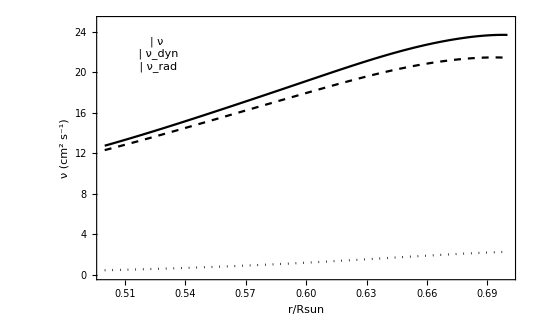
```mathematica
Plotν=-Graphics-;
```

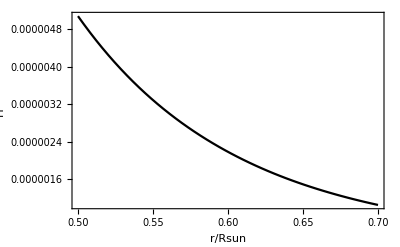

```mathematica
PlotPr
```